```mathematica
tmn[m_,n_,hp_]:=(2hp+m n-1+Sqrt[4hp(hp+m n-1)+(m-n)^2])/(n^2-1)
cmn[m_,n_,hp_]:=13-6(tmn[m,n,hp]+1/tmn[m,n,hp])
ljk[m_,n_,j_,k_,hp_]:=(j-k tmn[m,n,hp])/Sqrt[tmn[m,n,hp]]
li[m_,n_,hi_,hp_]:=Sqrt[hi+ljk[m,n,1,1,hp]^2/4]
Pmn[m_,n_,h1_,h2_,hp_]:=Product[(2li[m,n,h1,hp]-ljk[m,n,j,k,hp]/2)(-ljk[m,n,j,k,hp]/2)(2li[m,n,h2,hp]-ljk[m,n,j,k,hp]/2)(-ljk[m,n,j,k,hp]/2),{j,-m+1,m-1,2},{k,-n+1,n-1,2}]
itorAmn[m_,n_]:=DeleteCases[Flatten[Table[{a,b},{a,-m+1,m,1},{b,-n+1,n,1}],1],{x_,y_} /; (x==0&&y==0)||(x==m&&y==n)]
Bmn[m_,n_,hp_]:=Times@@(itorAmn[m,n]/.{{a_,b_}->ljk[m,n,a,b,hp]})
Amn[m_,n_,hp_]:=-12(tmn[m,n,hp]^(-1)-tmn[m,n,hp])/((m^2-1)tmn[m,n,hp]^(-1)-(n^2-1)tmn[m,n,hp])/Bmn[m,n,hp]
Rmn[m_,n_,h1_,h2_,hp_]:=If[hp==0&&m≥n,0,Amn[m,n,hp]Pmn[m,n,h1,h2,hp]]
gammamn[m_,n_,c_,h1_,h2_,hp_]:=Rmn[m,n,h1,h2,hp]/(c-cmn[m,n,hp])
genmntabinner[q_]:=Flatten[Table[{m,n},{m,1,q},{n,2,q}],1]
summn[lst_]:=If[lst=={},0,Plus@@Map[#[[1]]*#[[2]]&,lst]]
mod2prod[lst_]:=Plus@@Map[Mod[#[[1]]*#[[2]],2]&,lst]
genmntab[q_,l_]:=Select[Select[Tuples[genmntabinner[q],l],summn[#]==q&],mod2prod[#]==0&]
hpeff[lst_]:=summn[Drop[lst,-1]]
hpefflm1[lst_]:=summn[Drop[lst,-2]]
ceffl[l_,lst_,c_]:=If[l==1,c,cmn[lst[[-2]][[1]],lst[[-2]][[2]],hpefflm1[lst]]]
gammamlnl[l_,lst_,c_,h1_,h2_]:=gammamn[lst[[-1]][[1]],lst[[-1]][[2]],ceffl[l,lst,c],h1,h2,hpeff[lst]]
prodlvl[l_,lst_,c_,h1_,h2_]:=Times@@Table[gammamlnl[j,Take[lst,j],c,h1,h2],{j,1,l}]
chiq[q_,c_,h1_,h2_]:=Plus@@Flatten[Table[Expand[Map[prodlvl[l,#,c,h1,h2]&,genmntab[q,l]]],{l,q/2}]]
chiqfs[q_,c_,h1_,h2_]:=FullSimplify[chiq[q,c,h1,h2]]
expandinfty[q_,c_,h1_,h2_]:=ReplaceAll[Part[ReplaceAll[Series[chiq[q,c,h1,h2]/.{c->cinv^(-1),h1->h1inv^(-1),h2->h2inv^(-1)},{cinv,0,2},{h1inv,0,0},{h2inv,0,0}]//Normal,{h1inv->h1^(-1),h2inv->h2^(-1)}]//MonomialList,1],{cinv->c^(-1)}]//FullSimplify
flevel[q_,c_,h1_,h2_,z_]:=chiq[q,c,h1,h2]*z^q*Hypergeometric2F1[q,q,2q,z]
perlmutter[n_,c_,h1_,h2_,z_]:=Sum[expandinfty[q,c,h1,h2]*z^q*Hypergeometric2F1[q,q,2q,z],{q,2,n}]
fitzpatrick[c_,h1_,h2_,z_]:=2h1 h2 z^2 Hypergeometric2F1[2,2,4,z]/c+(2h1 h2 z^2 Hypergeometric2F1[2,2,4,z]/c)^2/2
diff[n_,c_,h1_,h2_,z_]:=perlmutter[n,c,h1,h2,z]-fitzpatrick[c,h1,h2,z]
```

```mathematica
chiqfs[2,c,h1,h2]
chiqfs[4,c,h1,h2]
chiqfs[6,c,h1,h2]
```

(2 h1 h2)/c

(2 h1 (1+5 h1) h2 (1+5 h2))/(5 c (22+5 c))

(h1 h2 (c^2 (1+14 h1) (1+14 h2)+84 h1^2 (-2+h2) (1+29 h2)-8 (5+7 h2 (7+3 h2))-28 h1 (14+h2 (25+171 h2))+6 c (15+14 h2 (7+8 h2)+98 h1 (1+8 h2+6 h2^2)+28 h1^2 (4+7 h2 (3+5 h2)))))/(63 c (-1+2 c) (22+5 c) (68+7 c))

```mathematica
chiqfs[8,c,h1,h2]
```

$Aborted

```mathematica
chiq[6,c,h1,h2]-(14h1^2+h1)(14h2^2+h2)/(63c(70c+29))-(4h1 h2(c(70h1^2+42h1+8)+29h1^2-57h1-2)(c(70h2^2+42h2+8)+29h2^2-57h2-2))/(3c(2c-1)(5c+22)(7c+68)(70c+29))//FullSimplify
```

0

```mathematica
expandinfty[4,c,h1,h2]
expandinfty[6,c,h1,h2]
```

(2 h1^2 h2^2)/c^2

(2 h1^2 h2^2)/(45 c^2)

```mathematica
expandinfty[8,c,h1,h2]
```

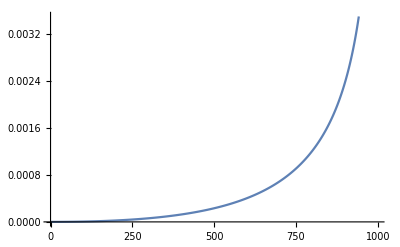

```mathematica
ListLinePlot[Table[flevel[2,1293834765577,17234,18265,z]+flevel[4,1293834765577,17234,18265,z]+fiz6[1293834765577,17234,18265,z]-(2*17234 * 18265*z^2 Hypergeometric2F1[2,2,4,z]/1293834765577)^2,{z,0.001,0.999,0.001}]]
```

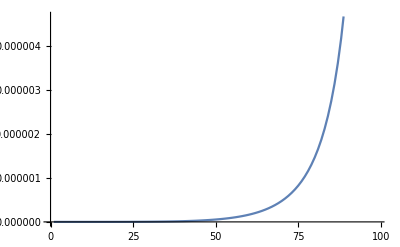

```mathematica
ListLinePlot[Table[(2*17234 * 18265*z^2 Hypergeometric2F1[2,2,4,z]/1293834765577)^2,{z,0.01,0.99,0.01}]]
```

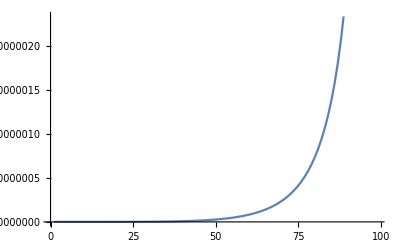

```mathematica
ListLinePlot[Table[(2*17234 * 18265*z^2 Hypergeometric2F1[2,2,4,z]/1293834765577)^2/2,{z,0.01,0.99,0.01}]]
```

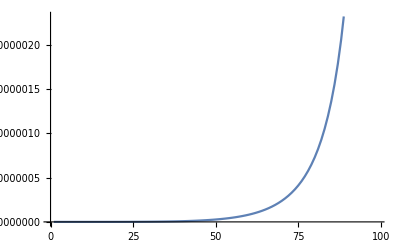

```mathematica
ListLinePlot[Table[flevel[4,1293834765577,17234,18265,z]+fiz6[1293834765577,17234,18265,z],{z,0.01,0.99,0.01}]]
```

```mathematica
fiz6[c_,h1_,h2_,z_]:=((14h1^2+h1)(14h2^2+h2)/(63c(70c+29))+(4h1 h2(c(70h1^2+42h1+8)+29h1^2-57h1-2)(c(70h2^2+42h2+8)+29h2^2-57h2-2))/(3c(2c-1)(5c+22)(7c+68)(70c+29)))*z^6*Hypergeometric2F1[6,6,12,z]
```

```mathematica
fiz6[c_,h1_,h2_,z_]:=((14h1^2+h1)(14h2^2+h2)/(63c(70c+29)))*z^6*Hypergeometric2F1[6,6,12,z]
```

```mathematica
1293834765577-17234*18265
```

1293519986567

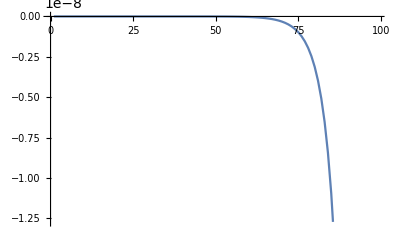

```mathematica
ListLinePlot[Table[flevel[4,1293834765577,17234,18265,z]+fiz6[1293834765577,17234,18265,z]-(2*17234 * 18265*z^2 Hypergeometric2F1[2,2,4,z]/1293834765577)^2/2,{z,0.01,0.99,0.01}]]
```

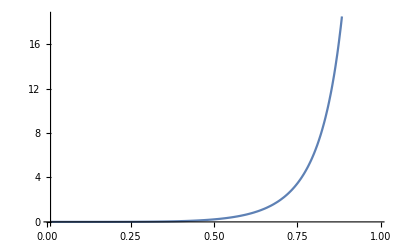

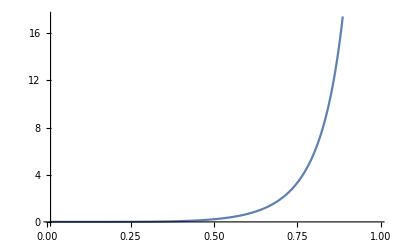

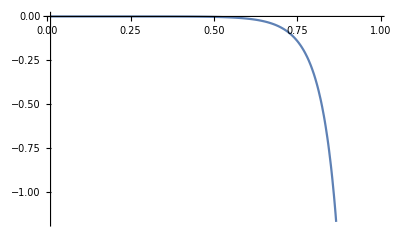

```mathematica
Plot[(z^2 Hypergeometric2F1[2,2,4,z])^2,{z,0.01,0.99}]
Plot[z^4 Hypergeometric2F1[4,4,8,z],{z,0.01,0.99}]
Plot[z^4 Hypergeometric2F1[4,4,8,z]-(z^2 Hypergeometric2F1[2,2,4,z])^2,{z,0.01,0.99}]
```

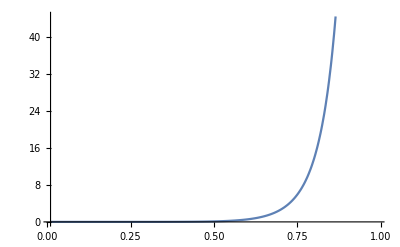

```mathematica
Plot[z^6 Hypergeometric2F1[6,6,12,z],{z,0.01,0.99}]
```

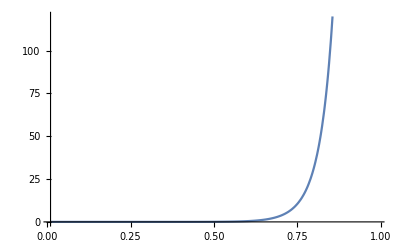

```mathematica
Plot[z^8 Hypergeometric2F1[8,8,16,z],{z,0.01,0.99}]
```

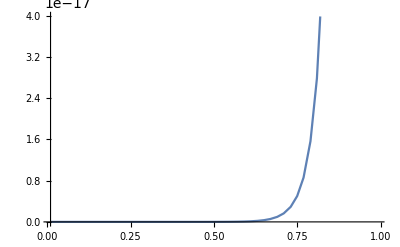

```mathematica
Plot[(2*17234 * 18265*z^2 Hypergeometric2F1[2,2,4,z]/1293834765577)^5/Factorial[5],{z,0.01,0.99}]
```

```mathematica
genmntab[6,3]
```

{{{1,2},{1,2},{1,2}}}